```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];

memoryTem=0;
For[i=1,i≤320,i++,{
For[j=1,j≤120,j++,{
memoryTem=data1[[(i-1)*240+j,3]];
data1[[(i-1)*240+j,3]]=data1[[(i-1)*240+(241-j),3]];
data1[[(i-1)*240+(241-j),3]]=memoryTem;
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]

Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[h[i],{i,320*240}],{320,240}],{80,240,4}],{240,80,4}],{80,80,12}];
h[p_]:=p;
If[Mask43[[80,80,12]]==76800,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

sumT=0;meanT=Mean@data1[[All,3]];
arrenged=Array[{#/#}&,{80,80,3}];
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-1)*4+2;
arrenged[[i,j,2]]=3*(j-1)+1.5;
sumT=0;
(*For[k=1,k<=12,k++,{sumT=sumT+data1[[Mask43[[i,j,k]],3]] }]*)
arrenged[[i,j,3]]=Sum[data1[[Mask43[[i,j,a]],3]],{a,12}]*(1/12);

arrenged[[i,j,3]]=meanT-arrenged[[i,j,3]];
  }]

}]
(*arrenged//MatrixForm*)
arrengedList=ArrayReshape[arrenged,{6400,3}];

ImageSizeLocal=250;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};
ListDensityPlot[data1,PlotRange->All,ColorFunction->colorsGoody,MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
ListDensityPlot[arrengedList,PlotRange->All,ColorFunction->colorsGoody,MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
```

{,}

C:\A\ Notes\PRG\W\gxIR000489.dat File exists

CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}

CheckPoint#2  - excellent

-Graphics-

-Graphics-

```mathematica
ii=-Graphics-;
res=TotalVariationFilter[ii,0.35,Method->"Poisson"];

Image[ImageAssemble[ImageTake[#,{120,200},{170,230}]&/@{ii,res}],Magnification->4]
```

-Graphics-

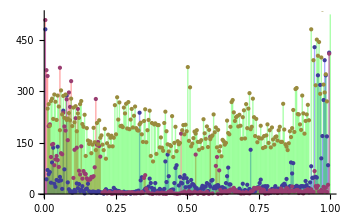

| Count | Mean | SD
Red | 232323. | 0.876449 | 0.310768
Green | 232323. | 0.482796 | 0.461359
Blue | 232323. | 0.0969889 | 0.272466

| Count | Mean | SD
 | 696969. | 0.485411 | 0.478698

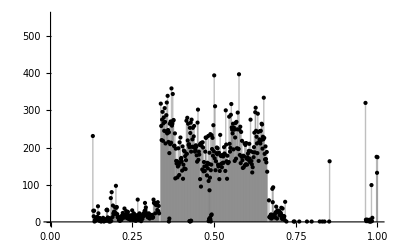

| Count | Mean | SD
 | 232323. | 0.485411 | 0.165864

```mathematica
x=Flatten[ImageData[-Graphics-],1];
{r,g,b}=Tally/@Transpose[x];
ListPlot[{b,r,g},Filling->Axis,FillingStyle->Table[i->Directive[Opacity[1/3],{Blue,Red,Green}[[i]]],{i,1,3}]]
stats[x_List]:=Block[{z=Join[x,{1,#[[1]]^2}&/@x,2],a,count,mean,sum,sumSquares},a=Transpose[z].z;
sum=a[[1,2]];
sumSquares=a[[2,4]];
count=a[[2,3]];
mean=sum/count;
{count,mean,Sqrt[sumSquares/count-mean^2]}];
TableForm[stats/@{r,g,b}//N,TableHeadings->{{"Red","Green","Blue"},{"Count","Mean","SD"}}]

TableForm[{stats[Join[r,g,b]]}//N,TableHeadings->{{},{"Count","Mean","SD"}}]
gray=Tally[Mean/@x];
ListPlot[gray,Filling->Axis,PlotStyle->Black,FillingStyle->Directive[Opacity[0.5],Gray]]
TableForm[{stats[gray]}//N,TableHeadings->{{},{"Count","Mean","SD"}}]
```